# Mathematica 入门 之 核心语法

## 基础语法

2021-08-11 陈可鉴

这里是一个最基础的介绍。学完本节课程，就可以根据自己的需要，选择「先学 MMA 中的数学」或是「继续学习 MMA 编程语法」了。

官方快速编程入门：
https://www.wolfram.com/language/fast-introduction-for-programmers/zh/
-Graphics-

笔记本界面

输入代码，按 ⇧+⌤ 进行计算
(Hello World!)

In[n] 和 Out[n] 标签会连续标记输入和输出. 
您可以使用 % 指定最近的输出，但是最好是定义一个变量.

笔记本是按单元组织的（右边的方括号），每个单元独立运行
可以选中、运行、复制粘贴，可以编组、排版

三种基本括号：( ) [ ] { }

## [ ] 方括号 代表函数作用于参数上

```mathematica
f[x]
```

f[x]

```mathematica
Sin[π]
```

0

英文逗号 用于分隔各个参数(Arguments)

```mathematica
f[a,b,c,d]
```

f[a,b,c,d]

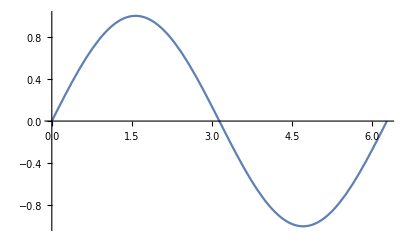

```mathematica
Plot[Sin[x],{x,0,2π}]
```

## ( ) 圆括号 代表运算的优先级（结合律）

数学优先级

```mathematica
Expand[3(a+b)]
```

3 a+3 b

```mathematica
Factor[3a+3b]
```

3 (a+b)

编程优先级

@ 代表函数的作用，f@x == f[x]

```mathematica
f@g@h
```

f[g[h]]

```mathematica
(f@g)@h
```

f[g][h]

## { } 花括号 代表列表

列表是有序的（区别于数学上的「集合」）

```mathematica
{1,2,3,4}=={4,3,2,1}
```

False

列表可以装任何东西


```mathematica
{1,x,"字符串",-Graphics-}
```

{1,x,字符串,-Graphics-}

列表有着丰富的含义

函数语法的组成部分

```mathematica
Table[i,{i,1,5}]
```

{1,2,3,4,5}

有序数对——向量

```mathematica
{a,b}.{c,d}
```

a c+b d

矩阵

```mathematica
{{a,b},
{c,d}}//MatrixForm
```

(a | b
c | d)

高维数组

```mathematica
Dimensions@{{{a,b},{c,d}},{{e,f},{g,h}}}
```

{2,2,2}

其他

```mathematica
{{"Alice",95},{"Bob",90},{"Chen",99}}
```

## 易错点：

圆括号( ) 只代表运算优先级，所有函数作用一律用 [ ] 中括号！！！

新手容易把函数 f(x) 在 Mathematica 里写成 f(x),但这就成了 f*x 的意思了

中文圆括号（ ）和英文圆括号( )易混淆，两者的高度和留白不同，注意区别！！！

中文标点符号在 Mathematica 中没有任何意义，当作普通变量符号

括号一定要匹配

内置函数

Wolfram 语言含有 5000 多个内置函数，均经过精心设计，风格统一，配有详尽文档。

## 内置函数的统一命名规则

英文短语
每个单词首字母大写（包括介词）
直接相连（无空格、无下划线）

举例：

```mathematica
{N,          If,Sin,Plot,Plot3D,PlotRangePadding,MomentOfInertia}
```

## 内置函数的统一语法

方括号，各个「参数 Arguments」用英文逗号分隔，「选项 Options」 放在最后

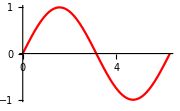

```mathematica
Plot[Sin[x],{x,0,2π},ImageSize->Small,PlotStyle->Red]
```

常见语法：变量范围

```mathematica
Plot[Sin[x],{x,0,2π}]
Integrate[Sin[x],{x,0,2π}]
Table[Sin[x],{x,0,2π}]
Table[Sin[x],{x,0,2π,1/2}]
```

-Graphics-

0

{0,Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6]}

{0,Sin[1/2],Sin[1],Sin[3/2],Sin[2],Sin[5/2],Sin[3],Sin[7/2],Sin[4],Sin[9/2],Sin[5],Sin[11/2],Sin[6]}

更多、更强大的内置函数，我们将在学习的过程中逐渐接触并熟悉。